## Second-order LCCDE

Many physical systems are described by second-order LCCDEs of the form

(ⅆ^2 y(t))/(ⅆ t^2)+a_1(ⅆy(t))/ⅆt+a_2 y(t)=b_1(ⅆx(t))/ⅆt+b_2 x(t)

where a_1, a_2, b_1, and b_2 are constant coefficients.

Depending on parameters there are 3 cases for roots s_1 and s_2:

1) a_1^2-4 a_2>0, roots will be real

2) a_1^2-4 a_2=0, roots will be real and identical

3) a_1^2-4 a_2<0, roots will be complex conjugates

#### It is more convenient to use three non-negative, physically meaningful parameters

α=a_1/2   – attenuation coefficient (Np/s),

ω_0=√a_2   – undamped natural frequency (rad/s)

ξ=α/ω_0=a_1/(2 √a_2)    – damping coefficient (unitless)

(a)  ξ>1   ⇒ overdamped response

(b)  ξ=1   ⇒ critically damped response

(c)  ξ<1   ⇒ underdamped response

### Second-order LCCDE with unit step input (x(t) = u(t))

#### HeavisideTheta[t] step function

HeavisideTheta[t] step function is used instead of UnitStep[t] function because derivative of UnitStep[t] undetermined.

```mathematica
UnitStep'[t]
```

Piecewise[{{Indeterminate, t==0}, {0, True}}]

```mathematica
?HeavisideTheta
```

Heaviside theta function θ(x), equal to 0 for x<0 and 1 for x>0

It can be used in integrals, integral transforms, and differential equations.

```mathematica
HeavisideTheta'[x]
```

DiracDelta[x]

#### Step input

x(t) = t

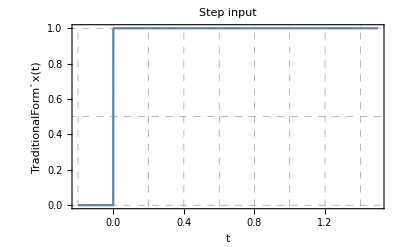

```mathematica
Clear[a1,a2,b1,b2,y,t,ξ];
(* step input *)
x1[t_]:=HeavisideTheta[t]
TraditionalForm[Row[{"x(t) = ",x1[t]}]]
(* plot of the input function *)
Plot[x1[t],{t,-0.2,1.5},Frame->True,Exclusions->None,PlotLabel->"Step input",FrameLabel->{t,"TraditionalForm`x(t)"},GridLinesStyle->Directive[Dashed,Gray,Thickness[0.001]],GridLines->{Range[-1,2,0.2],Range[-1,2,0.5]},PlotRange->All]
```

#### Second-order differential equation

```mathematica
(* declare LCCDE *)
lccde1=y''[t]+a1 y'[t]+a2 y[t]==b1 x1'[t]+b2 x1[t];
(* declare damping coefficient *)
ξ=a1/(2 √a2);
TraditionalForm[Row[{"LCCDE: ",lccde1}]]
```

LCCDE: a1 y'(t)+a2 y(t)+y''(t)==b1 t+b2 t

#### Three different sets of parameters are used in this example

a_1=80,a_2=400,b_1=80,b_2=400

a_1=40,a_2=400,b_1=40,b_2=400

a_1=20,a_2=400,b_1=20,b_2=400

#### Case 1. ξ>1, overdamped response

Note zero initial conditions in the differential equation: y(0) = 0, y'(0) = 0

a_1 = 80, a_2 = 400, b_1 = 80, b_2 = 400
ξ = a_1/(2 SqrtBox[SubscriptBox[a, 2]]) = 2 = 2. ⇒ Overdamped Case
LCCDE: y''(t)+80 y'(t)+400 y(t)==80 t+400 t
y = -(-3 ⅇ^((-40-20 √3) t)+2 √3 ⅇ^((-40-20 √3) t)-3 ⅇ^((20 √3-40) t)-2 √3 ⅇ^((20 √3-40) t)+6)/(6 (√3-2) (2+√3)) = 1-1/3 ⅇ^(-40 t) (2 √3 sinh(20 √3 t)+3 cosh(20 √3 t))

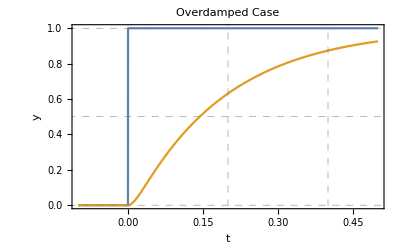

```mathematica
(* given parameters *)
a1=80; a2=400;b1=80;b2=400;
(* solution of LCCDE *)
lccdeS1=DSolve[{lccde1,y[0]==0,y'[0]==0},y[t],t,Assumptions->t>0];
(* display parameters, LCCDE, solution *)
TraditionalForm@Column[{
Row[{"a_1 = ",a1,", a_2 = ",a2,", b_1 = ",b1,", b_2 = ",b2}],
Row[{"ξ = a_1/(2 SqrtBox[SubscriptBox[a, 2]]) = ",ξ," = ",N@ξ," ⇒ ",If[ξ<1,"Underdamped Case",If[ξ==1,"Critically Damped Case","Overdamped Case"]]}],
Row[{"LCCDE: ",lccde1}],
Row[{"y = ",lccdeS1⟦1,1,2⟧," = ",FullSimplify@lccdeS1⟦1,1,2⟧}]
}]
(* display plot of the input and response *)
Plot[{UnitStep[t],(y[t]UnitStep[t])/.lccdeS1},{t,-0.1,0.5},Frame->True,Exclusions->None,PlotLabel->If[ξ<1,"Underdamped Case",If[ξ==1,"Critically Damped Case","Overdamped Case"]],FrameLabel->{t,"y"},GridLinesStyle->Directive[Dashed,Gray,Thickness[0.001]],GridLines->{Range[-1,2,0.2],Range[-1,2,0.5]},PlotRange->All]
```

#### Case 2. ξ=1, critically damped response

Note zero initial conditions in the differential equation: y(0) = 0, y'(0) = 0

a_1 = 40, a_2 = 400, b_1 = 40, b_2 = 400
ξ = a_1/(2 SqrtBox[SubscriptBox[a, 2]]) = 1 = 1. ⇒ Critically Damped Case
LCCDE: y''(t)+40 y'(t)+400 y(t)==40 t+400 t
y = ⅇ^(-20 t) (-20 t+ⅇ^(20 t)-1) = 1-ⅇ^(-20 t) (20 t+1)

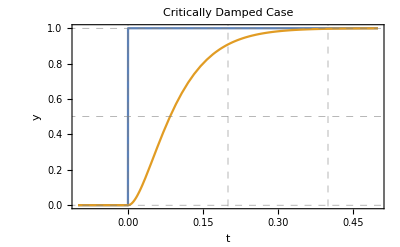

```mathematica
a1=40; a2=400;b1=40;b2=400;
lccdeS2=DSolve[{lccde1,y[0]==0,y'[0]==0},y[t],t,Assumptions->t>0];
TraditionalForm@Column[{
Row[{"a_1 = ",a1,", a_2 = ",a2,", b_1 = ",b1,", b_2 = ",b2}],
Row[{"ξ = a_1/(2 SqrtBox[SubscriptBox[a, 2]]) = ",ξ," = ",N@ξ," ⇒ ",If[ξ<1,"Underdamped Case",If[ξ==1,"Critically Damped Case","Overdamped Case"]]}],
Row[{"LCCDE: ",lccde1}],
Row[{"y = ",lccdeS2⟦1,1,2⟧," = ",FullSimplify@lccdeS2⟦1,1,2⟧}]
}]
Plot[{UnitStep[t],(y[t]UnitStep[t])/.lccdeS2},{t,-0.1,0.5},Frame->True,Exclusions->None,PlotLabel->If[ξ<1,"Underdamped Case",If[ξ==1,"Critically Damped Case","Overdamped Case"]],FrameLabel->{t,"y"},GridLinesStyle->Directive[Dashed,Gray,Thickness[0.001]],GridLines->{Range[-1,2,0.2],Range[-1,2,0.5]},PlotRange->All]
```

#### Case 3. ξ<1, underdamped response

Note zero initial conditions in the differential equation: y(0) = 0, y'(0) = 0

a_1 = 20, a_2 = 400, b_1 = 20, b_2 = 400
ξ = a_1/(2 SqrtBox[SubscriptBox[a, 2]]) = 1/2 = 0.5 ⇒ Underdamped Case
LCCDE: y''(t)+20 y'(t)+400 y(t)==20 t+400 t
y = 1/3 ⅇ^(-10 t) (3 ⅇ^(10 t) sin^2(10 √3 t)-√3 sin(10 √3 t)+3 ⅇ^(10 t) cos^2(10 √3 t)-3 cos(10 √3 t)) = 1-1/3 ⅇ^(-10 t) (√3 sin(10 √3 t)+3 cos(10 √3 t))

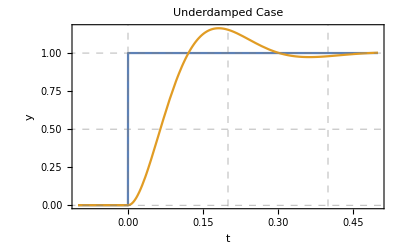

```mathematica
a1=20; a2=400;b1=20;b2=400;
lccdeS3=DSolve[{lccde1,y[0]==0,y'[0]==0},y[t],t,Assumptions->t>0];
TraditionalForm@Column[{
Row[{"a_1 = ",a1,", a_2 = ",a2,", b_1 = ",b1,", b_2 = ",b2}],
Row[{"ξ = a_1/(2 SqrtBox[SubscriptBox[a, 2]]) = ",ξ," = ",N@ξ," ⇒ ",If[ξ<1,"Underdamped Case",If[ξ==1,"Critically Damped Case","Overdamped Case"]]}],
Row[{"LCCDE: ",lccde1}],
Row[{"y = ",lccdeS3⟦1,1,2⟧," = ",FullSimplify@lccdeS3⟦1,1,2⟧}]
}]
Plot[{UnitStep[t],(y[t]UnitStep[t])/.lccdeS3},{t,-0.1,0.5},Frame->True,Exclusions->None,PlotLabel->If[ξ<1,"Underdamped Case",If[ξ==1,"Critically Damped Case","Overdamped Case"]],FrameLabel->{t,"y"},GridLinesStyle->Directive[Dashed,Gray,Thickness[0.001]],GridLines->{Range[-1,2,0.2],Range[-1,2,0.5]},PlotRange->All]
```

#### Summary

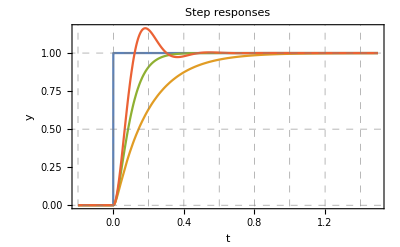

```mathematica
Plot[{UnitStep[t],(y[t]UnitStep[t])/.lccdeS1,(y[t]UnitStep[t])/.lccdeS2,(y[t]UnitStep[t])/.lccdeS3},{t,-0.2,1.5},Frame->True,Exclusions->None,PlotLabel->"Step responses",FrameLabel->{t,"y"},GridLinesStyle->Directive[Dashed,Gray,Thickness[0.001]],GridLines->{Range[-1,2,0.2],Range[-1,2,0.5]},PlotRange->All]
```